```mathematica
Integrate[1/(2p q)((Cos[ϕ]^2+Sin[ϕ]^2/p^2)Sin[θ]^2+Cos[θ]^2/q^2)^(-3/2)Sin[θ],{θ,0,π},Assumptions->{p>0,p<1,q>0,q<1}]
```

$Aborted

```mathematica
Integrate[p[θ],{θ,0,π},Assumptions->{q>0,q<1}]
```

1

```mathematica
Integrate[p[t]Sin[t],{t,0,θ},Assumptions->{q>0,q<1}]
```

1/(2 q)If[Cos[θ]^2+q^2 Sin[θ]^2≥0&&(-1+q^2) Cos[2 θ]≤1+q^2,q-(√2 q Cos[θ])/(√(1+q^2-(-1+q^2) Cos[2 θ])),Integrate[Sin[t]/((Cos[t]^2/q^2+Sin[t]^2)^(3/2)),{t,0,θ},Assumptions→q>0&&q<1&&!(Cos[θ]^2+q^2 Sin[θ]^2≥0&&(-1+q^2) Cos[2 θ]≤1+q^2)]]

```mathematica
P={θ,q}↦1/2(1-Cos[θ]/(√(q^2+(1-q^2)Cos[θ]^2)))
```

Function[{θ,q},1/2 (1-Cos[θ]/(√(q^2+(1-q^2) Cos[θ]^2)))]

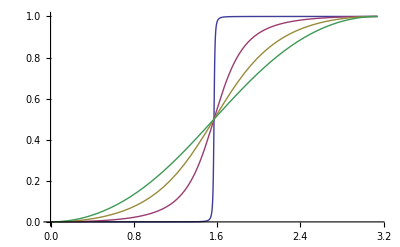

```mathematica
Plot[{P[θ,0.01],P[θ,0.3],P[θ,0.6],P[θ,0.9]},{θ,0,π}]
```

```mathematica
Solve[X==P[θ,q],θ]
```

Solve::verif: Potential solution {θ → ComplexInfinity} (possibly discarded by verifier) should be checked by hand. May require use of limits.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→-ArcCos[-(q √(1-4 X+4 X^2))/(√(q^2+4 X-4 q^2 X-4 X^2+4 q^2 X^2))]},{θ→ArcCos[-(q √(1-4 X+4 X^2))/(√(q^2+4 X-4 q^2 X-4 X^2+4 q^2 X^2))]},{θ→-ArcCos[(q √(1-4 X+4 X^2))/(√(q^2+4 X-4 q^2 X-4 X^2+4 q^2 X^2))]},{θ→ArcCos[(q √(1-4 X+4 X^2))/(√(q^2+4 X-4 q^2 X-4 X^2+4 q^2 X^2))]}}

```mathematica
FullSimplify[ArcCos[(q √(1-4 X+4 X^2))/(√(q^2+4 X-4 q^2 X-4 X^2+4 q^2 X^2))],Assumptions->{q>0,q<1,X>0,X<1/2}]
FullSimplify[ArcCos[-(q √(1-4 X+4 X^2))/(√(q^2+4 X-4 q^2 X-4 X^2+4 q^2 X^2))],Assumptions->{q>0,q<1,X>1/2,X<1}]
```

ArcCos[(q-2 q X)/(√(q^2 (1-2 X)^2-4 (-1+X) X))]

ArcCos[(q-2 q X)/(√(q^2 (1-2 X)^2-4 (-1+X) X))]

```mathematica
InverseX={X,q}↦ArcCos[(q (1-2 X))/(√(q^2 (1-2 X)^2+4 (1-X) X))]
```

Function[{X,q},ArcCos[(q (1-2 X))/(√(q^2 (1-2 X)^2+4 (1-X) X))]]

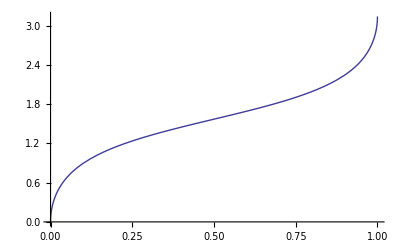

```mathematica
Plot[InverseX[X,0.6],{X,0,1}]
```

```mathematica
FullSimplify[InverseX[X,0]]
FullSimplify[InverseX[X,1]]
```

π/2

ArcCos[1-2 X]